```mathematica
nsol1 = NDSolve[
{-D[u[x,y], {x,2}]-D[u[x,y],{y,2}]== 5*(x*y)+NeumannValue[(x+y)-1*u[x,y], x == 0 || x== 1 || y== 0 || y == 1]},
u[x,y],{x,0,1},{y,0,1}]
```

{{u[x,y]→InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>][x,y]}}

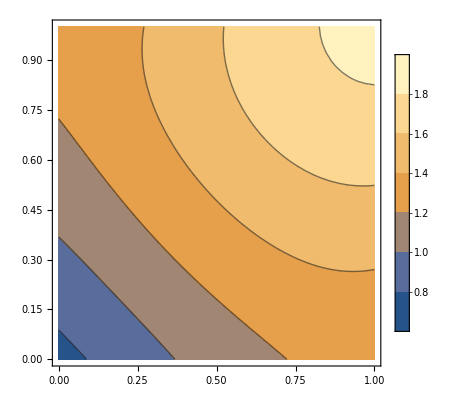

```mathematica
ContourPlot[Evaluate[u[x,y] /. nsol1],{x,0,1},{y,0,1},PlotLegends->Automatic]
```